# Field equations

These are the five field equations obtained from the varying the action with respect to the irreducible fields of the affine connection

```mathematica
eq1 =Subscript[B, 3]*(2*k +f[t]*g[t]+g[t]*h[t]+g'[t])-2*Subscript[B, 4]*(f[t]*g[t]-g[t]*h[t]+g'[t])+2*Subscript[D, 6]*η[t]*g[t]-2*Subscript[F, 3]*ψ[t]*ψ[t];
eq2=(Subscript[B, 3]-2*Subscript[B, 4])*η[t]*ψ[t]-Subscript[C, 1]*(2*h[t]*ψ[t]-ψ'[t]);
eq3=(Subscript[B, 3]+2*Subscript[B, 4])*η[t]*g[t]*ψ[t] + 2*Subscript[C, 1]*(k*ψ[t]-f[t]*g[t]*ψ[t]+4*g[t]*h[t]*ψ[t]-g[t]*ψ'[t]-ψ[t]*g'[t])+2*ψ[t]*ψ[t]*ψ[t]*(-Subscript[D, 1]+2*Subscript[D, 2]-Subscript[D, 3]);
eq4= Subscript[B, 3]*((η[t]*f[t]-η'[t])*ψ[t]+η[t]*(h[t]*ψ[t]-ψ'[t]))-2*Subscript[B, 4]*((η[t]*f[t]-η'[t])*ψ[t]-η[t]*(h[t]*ψ[t]+ψ'[t]))+Subscript[C, 1]*(-2*f[t]*h[t]*ψ[t]+f[t]*ψ'[t]+4*h[t]*h[t]*ψ[t]+2*ψ[t]*h'[t]-ψ''[t])+Subscript[D, 6]*η[t]*η[t]*ψ[t];
eq5=Subscript[B, 3]*(2*k+f[t]*g[t]+g[t]*h[t]+g'[t])*η[t]-2*Subscript[B, 4]*(f[t]*g[t]-g[t]*h[t]+g'[t])*η[t]+Subscript[C, 1]*(2*k*h[t]-2*f[t]*g[t]*h[t]-f[t]*g'[t]+4*g[t]*h[t]*h[t]-g[t]*f'[t]+2*g[t]*h'[t]-g''[t])+6*h[t]*ψ[t]*ψ[t]*(-Subscript[D, 1]+2*Subscript[D, 2]-Subscript[D, 3])+Subscript[D, 6]*η[t]*η[t]*g[t]-6*Subscript[F, 3]*η[t]*ψ[t]*ψ[t];
f[t_]:=0;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
FullSimplify[eq5]
```

2 g[t] (h[t] B_4+D_6 η[t])+B_3 (2 k+g[t] h[t]+g'[t])-2 (F_3 ψ[t]^2+B_4 g'[t])

(B_3-2 B_4) η[t] ψ[t]+C_1 (-2 h[t] ψ[t]+ψ'[t])

g[t] (B_3+2 B_4) η[t] ψ[t]-2 (D_1-2 D_2+D_3) ψ[t]^3+2 C_1 (ψ[t] (k+4 g[t] h[t]-g'[t])-g[t] ψ'[t])

D_6 η[t]^2 ψ[t]-B_3 ψ[t] η'[t]+2 B_4 ψ[t] η'[t]+B_3 η[t] (h[t] ψ[t]-ψ'[t])+2 B_4 η[t] (h[t] ψ[t]+ψ'[t])+C_1 (2 ψ[t] (2 h[t]^2+h'[t])-ψ''[t])

g[t] D_6 η[t]^2-6 h[t] (D_1-2 D_2+D_3) ψ[t]^2-6 F_3 η[t] ψ[t]^2+2 B_4 η[t] (g[t] h[t]-g'[t])+B_3 η[t] (2 k+g[t] h[t]+g'[t])+C_1 (2 h[t] (k+2 g[t] h[t])+2 g[t] h'[t]-g''[t])

```mathematica
FullSimplify[Solve[eq2==0,η[t]]]
```

{{η[t]→(C_1 (2 h[t] ψ[t]-ψ'[t]))/((B_3-2 B_4) ψ[t])}}

```mathematica
η[t_]:=(Subscript[C, 1] (2 h[t] ψ[t]-ψ'[t]))/((Subscript[B, 3]-2 Subscript[B, 4]) ψ[t]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
FullSimplify[eq5]
```

-2 F_3 ψ[t]^2+2 B_4 (g[t] h[t]-g'[t])+B_3 (2 k+g[t] h[t]+g'[t])+(2 g[t] C_1 D_6 (2 h[t] ψ[t]-ψ'[t]))/((B_3-2 B_4) ψ[t])

0

-2 (D_1-2 D_2+D_3) ψ[t]^3+(g[t] (B_3+2 B_4) C_1 (2 h[t] ψ[t]-ψ'[t]))/(B_3-2 B_4)+2 C_1 (ψ[t] (k+4 g[t] h[t]-g'[t])-g[t] ψ'[t])

(C_1 (2 h[t] ψ[t]-ψ'[t]) (h[t] (3 B_3^2-8 B_3 B_4+4 B_4^2+2 C_1 D_6) ψ[t]-C_1 D_6 ψ'[t]))/((B_3-2 B_4)^2 ψ[t])

-6 h[t] (D_1-2 D_2+D_3) ψ[t]^2+(2 B_4 C_1 (g[t] h[t]-g'[t]) (2 h[t] ψ[t]-ψ'[t]))/((B_3-2 B_4) ψ[t])+(B_3 C_1 (2 k+g[t] h[t]+g'[t]) (2 h[t] ψ[t]-ψ'[t]))/((B_3-2 B_4) ψ[t])+(6 C_1 F_3 ψ[t] (-2 h[t] ψ[t]+ψ'[t]))/(B_3-2 B_4)+(g[t] C_1^2 D_6 (-2 h[t] ψ[t]+ψ'[t])^2)/((B_3-2 B_4)^2 ψ[t]^2)+C_1 (2 h[t] (k+2 g[t] h[t])+2 g[t] h'[t]-g''[t])

```mathematica
FullSimplify[Solve[eq4==0,h[t]]]
```

{{h[t]→ψ'[t]/(2 ψ[t])},{h[t]→(C_1 D_6 ψ'[t])/((3 B_3^2-8 B_3 B_4+4 B_4^2+2 C_1 D_6) ψ[t])}}

```mathematica
k=0;
h[t_]:=ψ'[t]/(2 ψ[t]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
FullSimplify[eq5]
```

-2 F_3 ψ[t]^2+(B_3-2 B_4) g'[t]+(g[t] (B_3+2 B_4) ψ'[t])/(2 ψ[t])

0

-2 (D_1-2 D_2+D_3) ψ[t]^3+2 C_1 (-ψ[t] g'[t]+g[t] ψ'[t])

0

-3 (D_1-2 D_2+D_3) ψ[t] ψ'[t]-C_1 g''[t]+(g[t] C_1 ψ''[t])/ψ[t]

```mathematica
FullSimplify[DSolve[eq3==0,g[t],t]]
```

{{g[t]→ψ[t] (C[1]+-((D_1-2 D_2+D_3) ψ[K[1]])/C_1K[1]1t)}}

```mathematica
g[t_]:=ψ[t] ((k/ψ[K[1]]-((Subscript[D, 1]-2 Subscript[D, 2]+Subscript[D, 3]) ψ[K[1]])/Subscript[C, 1])K[1]1t);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
FullSimplify[eq5]
```

-(((B_3-2 B_4) (D_1-2 D_2+D_3)+2 C_1 F_3) ψ[t]^2)/C_1+1/2 (3 B_3-2 B_4) -((D_1-2 D_2+D_3) ψ[K[1]])/C_1K[1]1t ψ'[t]

0

0

0

«1 more identical outputs»

```mathematica
Print["Integro-differential equation with k->0"]
FullSimplify[eq1==0]
```

Integro-differential equation with k->0

(3 B_3-2 B_4) -((D_1-2 D_2+D_3) ψ[K[1]])/C_1K[1]1t ψ'[t]==(2 ((B_3-2 B_4) (D_1-2 D_2+D_3)+2 C_1 F_3) ψ[t]^2)/C_1

```mathematica
Print["Usando el cambio de variable ψ(t) = ϕ̇(t)"]
FullSimplify[ϕ''[t]*β*(-α*ϕ[t]) -γ(ϕ'[t])^2==0]
FullSimplify[DSolve[ϕ''[t]*β*(-α*ϕ[t]) -γ(ϕ'[t])^2==0,ϕ[t],t]]
FullSimplify[D[%,t]]
```

Usando el cambio de variable ψ(t) = ϕ̇(t)

γ ϕ'[t]^2+α β ϕ[t] ϕ''[t]==0

{{ϕ[t]→(t (α β+γ)-α β C[1])^((α β)/(α β+γ)) C[2]}}

{{ϕ'[t]→α β (t (α β+γ)-α β C[1])^(-γ/(α β+γ)) C[2]}}

```mathematica
ψ[t_]:= α β (t (α β+γ))^(-γ/(α β+γ)) ;
FullSimplify[g[t]]
```

α β (t (α β+γ))^(-γ/(α β+γ)) -(α β ((α β+γ) K[1])^(-γ/(α β+γ)) (D_1-2 D_2+D_3))/C_1K[1]1t

```mathematica
Print["The affine function g(t)"]
FullSimplify[g[t]]
FullSimplify[α β (t (α β+γ))^(-γ/(α β+γ))(-∫(α β (t (α β+γ))^(-γ/(α β+γ))(Subscript[D, 1]-2 Subscript[D, 2]+Subscript[D, 3]))/Subscript[C, 1] ⅆt)/.{Subscript[D, 1]->Subscript[C, 1]*α+2 Subscript[D, 2]-Subscript[D, 3]}]
Print["The affine function h(t)"]
FullSimplify[h[t]]
```

The affine function g(t)

α β (t (α β+γ))^(-γ/(α β+γ)) -(α β ((α β+γ) K[1])^(-γ/(α β+γ)) (D_1-2 D_2+D_3))/C_1K[1]1t

-α^2 β (t (α β+γ))^(-1+(2 α β)/(α β+γ))

The affine function h(t)

-γ/(2 t α β+2 t γ)

```mathematica
g[t_]:=-α^2 β (t (α β+γ))^(-1+(2 α β)/(α β+γ));
h[t_]:=-γ/(2 t α β+2 t γ);
```

```mathematica
Print["Parte temporal del Ricci"]
FullSimplify[-3*(h'[t]+h[t]*h[t])]
Print["El factor de escala afin del Ricci"]
FullSimplify[g'[t]+g[t]*h[t]+2*k]
```

Parte temporal del Ricci

-(3 γ (2 α β+3 γ))/(4 t^2 (α β+γ)^2)

El factor de escala afin del Ricci

-(α^2 β (2 α β-3 γ) (t (α β+γ))^((2 α β)/(α β+γ)))/(2 t^2 (α β+γ)^2)

```mathematica
FullSimplify[Solve[1/2==-γ/(αβ+γ),γ]]
```

{{γ→-αβ/3}}

```mathematica
Print["El factor de escala afin del Ricci"]
FullSimplify[g'[t]+g[t]*h[t]+2*k/.{γ->-αβ/3}]
```

El factor de escala afin del Ricci

-(9 α^2 β (t (-αβ/3+α β))^(-(6 α β)/(αβ-3 α β)) (αβ+2 α β))/(2 t^2 (αβ-3 α β)^2)

```mathematica
FullSimplify[Solve[2/3==-γ/(αβ+γ),γ]]
```

{{γ→-(2 αβ)/5}}

```mathematica
Print["El factor de escala afin del Ricci"]
FullSimplify[g'[t]+g[t]*h[t]+2*k/.{γ->-(2 αβ)/5}]
```

El factor de escala afin del Ricci

-(5 α^2 β (t (-(2 αβ)/5+α β))^((10 α β)/(-2 αβ+5 α β)) (3 αβ+5 α β))/(t^2 (2 αβ-5 α β)^2)

```mathematica
FullSimplify[(5*8*3^{10/3}/(9*5^{10/3}))]
```

{24/25 (3/5)^(1/3)}

```mathematica
FullSimplify[√(-24/25 (3/5)^(1/3)*α^(13/3)*β^(10/3))/.{ Subscript[B, 3]->1,Subscript[B, 4]->2}]
```

(2 √2 3^(2/3) √((-1)^(1/3) ((D_1-2 D_2+D_3)/C_1)^(13/3)))/(5 5^(1/6))

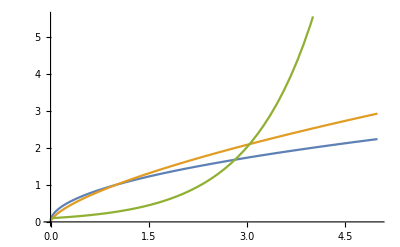

```mathematica
Plot[{t^(1/2),t^(2/3),0.1 ⅇ^t},{t,0,5}]
```

```mathematica
FullSimplify[D[t^(-γ/(αβ+γ)),t]]
```

-(t^(-2+αβ/(αβ+γ)) γ)/(αβ+γ)

```mathematica
FullSimplify[D[D[t^(-γ/(αβ+γ)),t],t]]
```

(t^(-3+αβ/(αβ+γ)) γ (αβ+2 γ))/(αβ+γ)^2

### Using the coupling constant explicitly

```mathematica
α=(Subscript[D, 1]-2 Subscript[D, 2]+Subscript[D, 3])/Subscript[C, 1];
β=(3 Subscript[B, 3]-2 Subscript[B, 4]);
γ=(2 ((Subscript[B, 3]-2 Subscript[B, 4]) (Subscript[D, 1]-2 Subscript[D, 2]+Subscript[D, 3])+2 Subscript[C, 1] Subscript[F, 3]))/Subscript[C, 1];
```

```mathematica
FullSimplify[h[t]]
FullSimplify[g[t]]
FullSimplify[ψ[t]]
Print["Parte temporal del Ricci"]
FullSimplify[-3*(h'[t]+h[t]*h[t])]
Print["El factor de escala afin del Ricci"]
FullSimplify[g'[t]+g[t]*h[t]+2*k]
```

-((B_3-2 B_4) (D_1-2 D_2+D_3)+2 C_1 F_3)/(t (5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 t C_1 F_3)

-((3 B_3-2 B_4) (D_1-2 D_2+D_3)^2 ((t (5 B_3-6 B_4) (D_1-2 D_2+D_3))/C_1+4 t F_3)^(((B_3+2 B_4) (D_1-2 D_2+D_3)-4 C_1 F_3)/((5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 C_1 F_3)))/C_1^2

((3 B_3-2 B_4) (D_1-2 D_2+D_3) ((t (5 B_3-6 B_4) (D_1-2 D_2+D_3))/C_1+4 t F_3)^(-(2 ((B_3-2 B_4) (D_1-2 D_2+D_3)+2 C_1 F_3))/((5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 C_1 F_3)))/C_1

Parte temporal del Ricci

-(6 ((3 B_3-4 B_4) (B_3-2 B_4) (D_1-2 D_2+D_3)^2+(9 B_3-14 B_4) C_1 (D_1-2 D_2+D_3) F_3+6 C_1^2 F_3^2))/(t (5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 t C_1 F_3)^2

El factor de escala afin del Ricci

-(2 (3 B_3-2 B_4) (D_1-2 D_2+D_3)^2 ((t (5 B_3-6 B_4) (D_1-2 D_2+D_3))/C_1+4 t F_3)^((2 (3 B_3-2 B_4) (D_1-2 D_2+D_3))/((5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 C_1 F_3)) (2 B_4 (D_1-2 D_2+D_3)-3 C_1 F_3))/(C_1 (t (5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 t C_1 F_3)^2)

```mathematica
DRic1 = h''[t] + 2*h[t]*h'[t];
DRic2= 2*g[t]*h[t]*h[t]-2*k*h[t]-h[t]*g'[t]+3*g[t]*h'[t];
DRic3=2*g[t]*h[t]*h[t]+4*k*h[t]+h[t]*g'[t]-g[t]*h'[t]-g''[t];
FullSimplify[DRic1]
FullSimplify[DRic2]
FullSimplify[DRic3]
```

-(4 ((3 B_3-4 B_4) (B_3-2 B_4) (D_1-2 D_2+D_3)^2+(9 B_3-14 B_4) C_1 (D_1-2 D_2+D_3) F_3+6 C_1^2 F_3^2))/(t^3 ((5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 C_1 F_3)^2)

-((2 (3 B_3-2 B_4) (D_1-2 D_2+D_3)^2 ((t (5 B_3-6 B_4) (D_1-2 D_2+D_3))/C_1+4 t F_3)^((2 (3 B_3-2 B_4) (D_1-2 D_2+D_3))/((5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 C_1 F_3)) ((B_3-2 B_4) (D_1-2 D_2+D_3)+2 C_1 F_3) ((9 B_3-10 B_4) (D_1-2 D_2+D_3)+6 C_1 F_3))/(C_1 (t (5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 t C_1 F_3)^3))

-(4 (3 B_3-2 B_4) (D_1-2 D_2+D_3)^2 ((t (5 B_3-6 B_4) (D_1-2 D_2+D_3))/C_1+4 t F_3)^((2 (3 B_3-2 B_4) (D_1-2 D_2+D_3))/((5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 C_1 F_3)) (2 B_4 (D_1-2 D_2+D_3)-3 C_1 F_3) ((B_3-2 B_4) (D_1-2 D_2+D_3)+2 C_1 F_3))/(C_1 (t (5 B_3-6 B_4) (D_1-2 D_2+D_3)+4 t C_1 F_3)^3)